```mathematica
(* PARAMETERS AND INTENSITY CALCULATION OF
  SCALAR SURFACE FROZEN WAVES FOR LOSSY OR LOSLESS MEDIA *)
```

```mathematica
(* INPUT IMAGE *)
Img=-Graphics-;
ImgBin=Abs[1-Reverse[ImageData[Binarize[Img]]]]; (* Input image binarized *)
pxH=Dimensions[ImgBin][[1]];(* Height of Img in pixels (x axis) *)
pxL=Dimensions[ImgBin][[2]]; (* Length of Img in pixels (z axis) *)
PathToF = NotebookDirectory[]<>"F.mtx";
Export[PathToF,ImgBin,"MTX"];(* Exporting discretized F *)
```

### SFW parameters ##################
ω    = 2.98046×10^15 Hz
irn  = 1.4+3.2×10^-7 ⅈ
λ0   = 632. nm
k0   = 9.94175×10^6 m^-1
k    = 1.39184×10^7+3.18136 ⅈ m^-1
Q    = 1.39157×10^7 m^-1
Q/k0 = 1.39972
Q/(irnR*k0) = 0.9998
pxL  = 163 px
pxH  = 43 px
L    = 6. cm
H    = 1.58282 cm
NN   = 10
P   = 458
Δ    = 150.506×10^-6

### Absorption coefficient and penetrarion depth ####
α_-NN = 6.36097 m^-1
δ_-NN = 0.157209 m
α_0  = 6.36145 m^-1
δ_0  = 0.157197 m
α_NN = 6.36193 m^-1
δ_NN = 0.157185 m

### LFWs displacement ####
ΔρLFW     = 8.64004×10^-6 m
Δρmin     = 17.2801×10^-6 m
Δρ        = 34.5602×10^-6 m
Δρ/ΔρLFW  = 4.
Δρ/Δρmin  = 2.
LFW/pixel = 10.6512

### Axicon angles ###########
α0_-NN = 1.34432°
α0_0  = 1.14593°
α0_NN  = 0.905072°

### Discretized F ###########

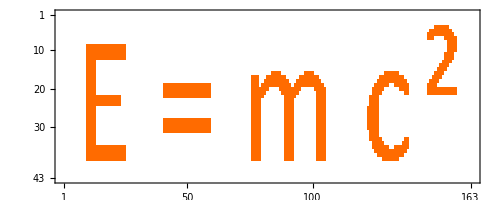

```mathematica
(* SFW PARAMETERS *)
(* General *)
l0=632. 10^-9;
k0=2π/l0;
ω=k0 299792458;
nr=1.4;
ni=0.32 10^-6;
irn=nr+ⅈ ni;
Q=0.9998nr*k0;
L=0.06;
NN=10;
P=Ceiling[H/Δρ];
H=L(pxH/pxL);

(* Wavenumbers *)
k=k0 irn;
βr[q_]:=Q+2π q/L
βi[q_]:=βr[q]ni/nr
β[q_]:=βr[q](1+ⅈ ni/nr)
hr[q_]:=Re[√(k^2-β[q]^2)]
hi[q_]:=Im[√(k^2-β[q]^2)]
h[q_]:=hr[q]+ⅈ hi[q]

(* Parameter that should be << 1 to ensure the validity of FT approximation *)
Δ=4π NN/(L Q);

(* Radial displacement of LFWs *)
ΔρLFW=2.405/hr[0]; (* spot *)
spot = ΔρLFW; (* spot *)
Δρmin = 2*ΔρLFW;(* 2*ΔρLFW, minimmum recomended separation *)
Δρ=2.0*Δρmin;(* A chosen radial separation *)

(* Print of general parameters *)
Print["### SFW parameters ##################\n",
"ω    = ",ω," Hz","\n","irn  = ",irn,"\n","λ0   = ",l0*10^9," nm","\n","k0   = ",N[k0,10]," m^-1","\n","k    = ",N[k,10]," m^-1","\n", "Q    = ",N[Q,10]," m^-1","\n","Q/k0 = ",Q/k0,"\n","Q/(irnR*k0) = ",Q/(nr*k0),"\n", "pxL  = ",pxL," px","\n", "pxH  = ",pxH," px","\n","L    = ",L*10^2," cm","\n", "H    = ",H*10^2," cm","\n","NN   = ",NN,"\n", "P   = ",P,"\n", "Δ    = ",EngineeringForm[Δ]]
If[ni==0.,Print["### Absorption coefficient and penetrarion depth ####\n none"],
Print["### Absorption coefficient and penetrarion depth ####\n",
"α_-NN = ",2βi[-NN]," m^-1","\n","δ_-NN = ",N[1/(2βi[-NN])]," m","\n","α_0  = ",2βi[0]," m^-1","\n","δ_0  = ",N[1/(2βi[0])]," m","\n","α_NN = ",2βi[NN]," m^-1","\n","δ_NN = ",N[1/(2βi[NN])]," m"]]
Print["### LFWs displacement ####\n",
"ΔρLFW     = ",EngineeringForm[ΔρLFW]," m","\n","Δρmin     = ",EngineeringForm[Δρmin]," m","\n","Δρ        = ",EngineeringForm[Δρ]," m","\n","Δρ/ΔρLFW  = ",Δρ/ΔρLFW,"\n","Δρ/Δρmin  = ",Δρ/Δρmin,"\n", "LFW/pixel = ", N[P/pxH]]
If[ni==0.,
Print["### Axicon angles ###########\n",
"α0_-NN = ",(180/Pi)ArcSin[h[-NN]/k],"°","\n","α0_0  = ",(180/Pi)ArcSin[h[0]/k],"°","\n","α0_NN  = ",(180/Pi)ArcSin[h[NN]/k],"°"],
Print["### Axicon angles ###########\n",
"α0_-NN = ",(180/Pi)ArcCos[βi[-NN]/(k0 ni)],"°","\n","α0_0  = ",(180/Pi)ArcCos[βi[0]/(k0 ni)],"°","\n","α0_NN  = ",(180/Pi)ArcCos[βi[NN]/(k0 ni)],"°"]]
Print["### Discretized F ###########"]
MatrixPlot[Reverse[ImgBin]]
```

```mathematica
(* Generating a string to run the sfwi C++ application *)
PathToSfwi=NotebookDirectory[]<>"sfwi.exe";
FileIn=PathToF;
FileOut=NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[3Ld4].mtx";
CutAxis="z";
CutValue=3.L/4.;
xmin=0;
xmax=H;
xpoints=2P;
ymin=0.;
ymax=H/2.;
ypoints=P;
zmin=0.;
zmax=L;
zpoints=pxL;
IsNonresistant=0; (* 0 for false, 1 for true *)
CppString=StringJoin["\"",ToString[PathToSfwi],"\" ",ToString[DecimalForm[nr]]," ",ToString[DecimalForm[ni]]," ",ToString[DecimalForm[l0]]," ",ToString[DecimalForm[Q]]," ",ToString[NN]," ",ToString[DecimalForm[L]]," ",ToString[P]," ",ToString[CutAxis]," ",ToString[DecimalForm[CutValue]]," ",ToString[DecimalForm[xmin]]," ",ToString[DecimalForm[xmax]]," ",ToString[xpoints]," ",ToString[DecimalForm[ymin]]," ",ToString[DecimalForm[ymax]]," ",ToString[ypoints]," ",ToString[DecimalForm[zmin]]," ",ToString[DecimalForm[zmax]]," ",ToString[zpoints]," ",ToString[IsNonresistant]," \"",ToString[FileIn],"\" \"",ToString[FileOut],"\""];
```

```mathematica
(* To calculate the intensities you must do one of the followings *)
```

```mathematica
(* Evaluate this cell to run the C++ application inside Wolfram Mathematica with 'RunProcess[]' *)
(* Disadvantages: Mathematica costs too much RAM and you can not use this notebook while the process is running *)
RunProcess[{PathToSfwi, ToString[DecimalForm[nr]], ToString[DecimalForm[ni]], ToString[DecimalForm[l0]], ToString[DecimalForm[Q]], ToString[NN], ToString[DecimalForm[L]], ToString[P], ToString[CutAxis], ToString[DecimalForm[CutValue]], ToString[DecimalForm[xmin]], ToString[DecimalForm[xmax]], ToString[xpoints], ToString[DecimalForm[ymin]], ToString[DecimalForm[ymax]], ToString[ypoints], ToString[DecimalForm[zmin]], ToString[DecimalForm[zmax]], ToString[zpoints],ToString[IsNonresistant], FileIn,FileOut},"StandardOutput"];
```

```mathematica
(* Evaluate this cell to run the C++ application inside Wolfram Mathematica with 'StartProcess[]' *)
(* Advantages: you are free to use Mathematica while the process is running *)
(* Disadvantages: Mathematica costs too much RAM *)
StartProcess[{PathToSfwi, ToString[DecimalForm[nr]], ToString[DecimalForm[ni]], ToString[DecimalForm[l0]], ToString[DecimalForm[Q]], ToString[NN], ToString[DecimalForm[L]], ToString[P], ToString[CutAxis], ToString[DecimalForm[CutValue]], ToString[DecimalForm[xmin]], ToString[DecimalForm[xmax]], ToString[xpoints], ToString[DecimalForm[ymin]], ToString[DecimalForm[ymax]], ToString[ypoints], ToString[DecimalForm[zmin]], ToString[DecimalForm[zmax]], ToString[zpoints],ToString[IsNonresistant], FileIn,FileOut}];
```

```mathematica
(* Paste the string below in prompt command to execute C++ application externally *)
(* Advantages: costs about 10 MB of RAM and you are free to close Mathematica *)
Print[CppString]
```